Assignment 2
ELEC-E7460 Modeling and Simulation, fall 2018
Adam Ilyas 725819

## Question 1 single-class M/G/1 PS queue. a)

Consider the single-class M/G/1 PS queue. 

Assume first that the service times are exponentially distributed with mean 1. 

Simulate the system for λ = {0.2, 0.5, 0.8} and estimate the mean delay of the jobs. 

Also, determine the 95% confidence intervals.

```mathematica
Needs["HypothesisTesting`"]
simulatorPS[la_,mu_,iniTrans_,simuLen_]:=Module[{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i},
simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
If[Length[joblist]>0,
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]],
joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
joblist=Append[joblist,{simTime,RandomVariate[ExponentialDistribution[mu]]}];
(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]];
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]
```

Service time ~ Exp(mu = 1)
Arrival time ~Exp(λ )

Simulate the system for λ = {0.2, 0.5, 0.8} and estimate the mean delay of the jobs.

```mathematica
For[i=1,i<=Length[lambdas],i++, 
la = lambdas[[i]];
res = Table[simulatorPS[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]];
ci = MeanCI[res[[All,2]]];
Print[StringForm["When λ = ``, Mean: ``, 95% Confidence Interval = ``",la,NumberForm[mean, 5], ci]]
]
```

When λ = 0.2, Mean: 1.2577, 95% Confidence Interval = {1.24539,1.26992}

When λ = 0.5, Mean: 1.9946, 95% Confidence Interval = {1.94877,2.04039}

When λ = 0.8, Mean: 4.9683, 95% Confidence Interval = {4.76486,5.17172}

## Question 1 b) single-class M/G/1 PS queue with hyperexponential service times

Assume now that the service times obey the hyperexponential distribution with two
phases representing long and short service times. More precisely, consider a hyperexponential
distribution with two phases γ 1 and γ 2 with weight parameter p with the following values

γ 1 = 0.1 
γ 2 = 10 
weight parameter p = 0.0909091

Repeat the same simulation as in a)-part and compare the results. Note that with these
parameters the service times have 17 times greater variance than with exponential distribution and 
recall the discussion on the lectures on impact of service times and scheduling
discipline. What do you observe? Are you able to explain your observations?

```mathematica
simulatorPShyperexp[la_,mu_,iniTrans_,simuLen_]:=Module[
{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i, 

(* Hyperexponential distribution parameter *)
gamma1, gamma2, weightParameter

},
gamma1 = 0.1; gamma2 = 10; weightParameter=0.0909091; 

simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
If[Length[joblist]>0,
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]],
joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
(* joblist=Append[joblist,{simTime,RandomVariate[ExponentialDistribution[mu]]}]; *)
joblist = Append[joblist,{simTime,RandomVariate[HyperexponentialDistribution[{weightParameter,1-weightParameter},{gamma1,gamma2}]]}];

(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]];
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]
```

For hyperexponential Service times, the confidence interval larger as compared to the queue simulation with 
exponential service times.

```mathematica
For[i=1,i<=Length[lambdas],i++, 
la = lambdas[[i]];
res = Table[simulatorPShyperexp[la,1,2000,200000],{10}];
mean = Mean[res[[All,2]]];
ci = MeanCI[res[[All,2]]];
Print[StringForm["When λ = ``, Mean: ``, 95% Confidence Interval = ``",la,NumberForm[mean, 5], ci]]
]
```

When λ = 0.2, Mean: 1.2519, 95% Confidence Interval = {1.2366,1.26729}

When λ = 0.5, Mean: 2.009, 95% Confidence Interval = {1.96898,2.04908}

When λ = 0.8, Mean: 4.9208, 95% Confidence Interval = {4.78287,5.05881}

Recall: For exponential Service times below (part 1a)

```mathematica
For[i=1,i<=Length[lambdas],i++, 
la = lambdas[[i]];
res = Table[simulatorPS[la,1,2000,200000],{10}];
mean = Mean[res[[All,2]]];
ci = MeanCI[res[[All,2]]];
Print[StringForm["When λ = ``, Mean: ``, 95% Confidence Interval = ``",la,NumberForm[mean, 5], ci]]
]
```

When λ = 0.2, Mean: 1.2481, 95% Confidence Interval = {1.24219,1.25407}

When λ = 0.5, Mean: 2.0022, 95% Confidence Interval = {1.98804,2.01628}

When λ = 0.8, Mean: 4.9827, 95% Confidence Interval = {4.91411,5.05121}

## Question 2a) Modified single-class M/G/1 PS simulator to simulate both FIFO discipline and the SRPT discipline.

Your task is to simulate the M/G/1 queue with two different service time distributions and
compare the performance of the three disciplines (FIFO, PS, SRPT) to each other. 

Let us fix the mean service time as 1/μ = 1 and then the load ρ = λ.

Assume first that the service times obey the exponential distribution with mean 1/μ = 1.
Simulate the system for λ = {0.4, 0.6, 0.8} and estimate the mean delay together with its
95% confidence interval.

```mathematica
simulatorFIFO[la_,mu_,iniTrans_,simuLen_]:=
Module[{simTime,res,queueLength,meanqlen,prevEvTime,nextArr,nextDep,nofsamples,i,serviceTime,totalService, queue},
simTime=0;
nextArr=RandomVariate[ExponentialDistribution[la]];
nextDep=Infinity;
queueLength=0;
serviceTime=0;
totalService=0;
nofsamples=0;
meanqlen=0;
While[simTime≤simuLen,
(* Upon arrival *)
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
(* the system state,i.e.the queue length is incremented by one:X t=X t+1 *)
queueLength+=1;
(* if the system is empty upon the arrival *)
(* generate the departure time of the customer,t+S,where S is a sample from the service time distribution *)
If[queueLength==1,
{serviceTime=RandomVariate[ExponentialDistribution[mu]];
(* departure = t+S *)
nextDep=simTime + serviceTime;
},
{serviceTime=0;
}];
(* generate the arrival instant of the next customer,t+I *) 
(* where I is the interarrival time (drawn from Exp(l) distribution) *)
nextArr=simTime + RandomVariate[ExponentialDistribution[la]];
(* collect statistics *)
If[simTime>iniTrans,
{totalService+=serviceTime;
nofsamples+=1;
meanqlen+=queueLength*(simTime-prevEvTime);}]
},
(* Event handling upon the departure of a customer *)
(* If nextDep < nextArr *)
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep;(*move time to new event*)

(*update state*)
queueLength-=1;
(* if there are customers left in the system *) 
(* generate the departure time of the customer to be served next,t+S *)
(* where S is a sample from the service time distribution *)
If[queueLength != 0,
{serviceTime=RandomVariate[ExponentialDistribution[mu]];
nextDep=serviceTime+simTime;
},
{serviceTime=0;
}];
If[simTime>iniTrans,
{totalService+=serviceTime;
meanqlen+=queueLength*(simTime-prevEvTime);
}];
}];
(*Print[queueLength]*)
];
(* Return *)
{meanqlen/(la*simuLen),totalService/nofsamples}
];
```

```mathematica
simulatorPS[la_,mu_,iniTrans_,simuLen_]:=Module[{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i},
simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
If[Length[joblist]>0,
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]],
joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
joblist=Append[joblist,{simTime,RandomVariate[ExponentialDistribution[mu]]}];
(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]];
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]
```

SRPT is not a big change from PS, 

Instead of serving all the remaining jobs, 

we only serve the job with the shortest remaining service time left

```mathematica
simulatorSRPT[la_,mu_,iniTrans_,simuLen_]:=Module[{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i},
simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the job with the shortest remaining time left *)
If[Length[joblist]>0,
joblist[[1,2]] = joblist[[1,2]] - (simTime-prevEvTime)
,joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
joblist=Append[joblist,{simTime,RandomVariate[ExponentialDistribution[mu]]}];
(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the job with shortest remaining time left *)
joblist[[1,2]] = joblist[[1,2]] - (simTime-prevEvTime) ;
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]
```

```mathematica
Needs["HypothesisTesting`"]

loads = {0.4,0.6,0.8};
For[i=1,i<=Length[loads],i++, 
la = loads[[i]];

d= "FIFO";
res = Table[simulatorFIFO[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]]; ci = MeanCI[res[[All,2]]];
Print["When λ = ``", la];
Print[StringForm["Discipline: ``, Mean Delay: ``, 95% Confidence Interval = ``",d,NumberForm[mean, 5], ci]];

d = "PS";
res = Table[simulatorPS[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]]; ci = MeanCI[res[[All,2]]];
Print[StringForm["Discipline: ``, Mean Delay: ``, 95% Confidence Interval = ``",d,NumberForm[mean, 5], ci]];

d = "SRPT";
res = Table[simulatorSRPT[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]]; ci = MeanCI[res[[All,2]]];
Print[StringForm["Discipline: ``, Mean Delay: ``, 95% Confidence Interval = ``",d,NumberForm[mean, 5], ci]];
]
```

When λ = ``0.4

Discipline: FIFO, Mean Delay: 2.5039, 95% Confidence Interval = {2.48541,2.52243}

Discipline: PS, Mean Delay: 1.6698, 95% Confidence Interval = {1.6388,1.70088}

Discipline: SRPT, Mean Delay: 1.3894, 95% Confidence Interval = {1.36088,1.41799}

When λ = ``0.6

Discipline: FIFO, Mean Delay: 1.6762, 95% Confidence Interval = {1.66237,1.69009}

Discipline: PS, Mean Delay: "<2.4347>", 95% Confidence Interval = {2.37107, 2.49829}

Discipline: SRPT, Mean Delay: 1.2858, 95% Confidence Interval = {1.26539,1.30612}

When λ = ``0.8

Discipline: FIFO, Mean Delay: 1.2534, 95% Confidence Interval = {1.24877,1.25803}

Discipline: PS, Mean Delay: 4.9521, 95% Confidence Interval = {4.74702,5.15716}

Discipline: SRPT, Mean Delay: 0.90992, 95% Confidence Interval = {0.882442,0.937395}

## Question 2b) PS, FIFO, SRPT single-class M/G/1 PS simulator service times obey a hyperexponential distribution with 2 phases

```mathematica
simulatorFIFOhyperexp[la_,iniTrans_,simuLen_]:=
Module[{simTime,res,queueLength,meanqlen,prevEvTime,nextArr,nextDep,nofsamples,i,serviceTime,totalService, queue, 
gamma1, gamma2, weightParameter},
gamma1 = 0.1; gamma2 = 10; weightParameter=0.0909091; 
simTime=0;
nextArr=RandomVariate[ExponentialDistribution[la]];
nextDep=Infinity;
queueLength=0;
serviceTime=0;
totalService=0;
nofsamples=0;
meanqlen=0;
While[simTime≤simuLen,
(* Upon arrival *)
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
(* the system state,i.e.the queue length is incremented by one:X t=X t+1 *)
queueLength+=1;
(* if the system is empty upon the arrival *)
(* generate the departure time of the customer,t+S,where S is a sample from the service time distribution *)
If[queueLength==1,
{serviceTime= RandomVariate[HyperexponentialDistribution[{weightParameter,1-weightParameter},{gamma1,gamma2}]];
(* departure = t+S *)
nextDep=simTime + serviceTime;
},
{serviceTime=0;
}];
(* generate the arrival instant of the next customer,t+I *) 
(* where I is the interarrival time (drawn from Exp(l) distribution) *)
nextArr=simTime + RandomVariate[ExponentialDistribution[la]];
(* collect statistics *)
If[simTime>iniTrans,
{totalService+=serviceTime;
nofsamples+=1;
meanqlen+=queueLength*(simTime-prevEvTime);}]
},
(* Event handling upon the departure of a customer *)
(* If nextDep < nextArr *)
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep;(*move time to new event*)

(*update state*)
queueLength-=1;
(* if there are customers left in the system *) 
(* generate the departure time of the customer to be served next,t+S *)
(* where S is a sample from the service time distribution *)
If[queueLength != 0,
{serviceTime= RandomVariate[HyperexponentialDistribution[{weightParameter,1-weightParameter},{gamma1,gamma2}]];
nextDep=serviceTime+simTime;
},
{serviceTime=0;
}];
If[simTime>iniTrans,
{totalService+=serviceTime;
meanqlen+=queueLength*(simTime-prevEvTime);
}];
}];
(*Print[queueLength]*)
];
(* Return *)
{meanqlen/(la*simuLen),totalService/nofsamples}
];

simulatorPShyperexp[la_,iniTrans_,simuLen_]:=Module[{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i,
gamma1,gamma2, weightParameter},
gamma1 = 0.1; gamma2 = 10; weightParameter=0.0909091;
simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
If[Length[joblist]>0,
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]],
joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
joblist=Append[joblist,{simTime,RandomVariate[HyperexponentialDistribution[{weightParameter,1-weightParameter},{gamma1,gamma2}]]}];
(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]];
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]

simulatorSRPThyperexp[la_,iniTrans_,simuLen_]:=Module[{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i,
gamma1, gamma2, weightParameter},
gamma1 = 0.1; gamma2 = 10; weightParameter=0.0909091;
simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the job with the shortest remaining time left *)
If[Length[joblist]>0,
joblist[[1,2]] = joblist[[1,2]] - (simTime-prevEvTime)
,joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
joblist=Append[joblist,{simTime,RandomVariate[HyperexponentialDistribution[{weightParameter,1-weightParameter},{gamma1,gamma2}]]}];
(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the job with shortest remaining time left *)
joblist[[1,2]] = joblist[[1,2]] - (simTime-prevEvTime) ;
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]
```

```mathematica
Needs["HypothesisTesting`"]

loads = {0.4,0.6,0.8};
For[i=1,i<=Length[loads],i++, 
la = loads[[i]];

d= "FIFO (Hyperexponential Service times)";
res = Table[simulatorFIFOhyperexp[la,2000,20000],{10}];
mean = Mean[res[[All,2]]]; ci = MeanCI[res[[All,2]]];
Print["When λ = ``", la];
Print[StringForm["Discipline: ``, Mean Delay: ``, 95% Confidence Interval = ``",d,NumberForm[mean, 5], ci]];

d = "PS (Hyperexponential Service times)";
res = Table[simulatorPShyperexp[la,2000,20000],{10}];
mean = Mean[res[[All,2]]]; ci = MeanCI[res[[All,2]]];
Print[StringForm["Discipline: ``, Mean Delay: ``, 95% Confidence Interval = ``",d,NumberForm[mean, 5], ci]];

d = "SRPT (Hyperexponential Service times)";
res = Table[simulatorSRPThyperexp[la,2000,20000],{10}];
mean = Mean[res[[All,2]]]; ci = MeanCI[res[[All,2]]];
Print[StringForm["Discipline: ``, Mean Delay: ``, 95% Confidence Interval = ``",d,NumberForm[mean, 5], ci]];
]
```

When λ = ``0.4

Discipline: FIFO (Hyperexponential Service times), Mean Delay: 2.4924, 95% Confidence Interval = {2.47442,2.5104}

Discipline: PS (Hyperexponential Service times), Mean Delay: 1.6311, 95% Confidence Interval = {1.53437,1.72792}

Discipline: SRPT (Hyperexponential Service times), Mean Delay: 1.1976, 95% Confidence Interval = {1.14057,1.25471}

When λ = ``0.6

Discipline: FIFO (Hyperexponential Service times), Mean Delay: 1.6733, 95% Confidence Interval = {1.6636,1.68298}

Discipline: PS (Hyperexponential Service times), Mean Delay: 2.5578, 95% Confidence Interval = {2.40994,2.70569}

Discipline: SRPT (Hyperexponential Service times), Mean Delay: 1.2599, 95% Confidence Interval = {1.18239,1.33745}

When λ = ``0.8

Discipline: FIFO (Hyperexponential Service times), Mean Delay: 1.2599, 95% Confidence Interval = {1.24886,1.271}

Discipline: PS (Hyperexponential Service times), Mean Delay: 4.4229, 95% Confidence Interval = {3.81458,5.03125}

Discipline: SRPT (Hyperexponential Service times), Mean Delay: 1.3097, 95% Confidence Interval = {1.24713,1.37222}

## Question 2c) Compare the results. What do you observe?

c)  To gain more insight you may also use the results of PS as a reference and evaluate the ratio of the delays for FIFO and SRPT relative
to PS. If you want to visualize the results in a plot, you can of course simulate more load
values. Note that with these parameters the service times have almost 17 times greater
variance than with the exponential distribution and recall the discussion on the lectures on
impact of service times and scheduling discipline.

```mathematica
data = {{},{},{},{},{},{}};

loads = {0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
For[i=1,i<=Length[loads],i++, 
la = loads[[i]];

res = Table[simulatorFIFO[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]]; 
data[[1]] = Append[data[[1]] , {la, mean}];

res = Table[simulatorPS[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]];
data[[2]]  = Append[data[[2]] , {la, mean}];

res = Table[simulatorSRPT[la,1,2000,20000],{10}];
mean = Mean[res[[All,2]]];
data[[3]] = Append[data[[3]] , {la, mean}];

res = Table[simulatorFIFOhyperexp[la,2000,20000],{10}];
mean = Mean[res[[All,2]]]; 
data[[4]] = Append[data[[4]] , {la, mean}];

res = Table[simulatorPShyperexp[la,2000,20000],{10}];
mean = Mean[res[[All,2]]];
data[[5]]  = Append[data[[5]] , {la, mean}];

res = Table[simulatorSRPThyperexp[la,2000,20000],{10}];
mean = Mean[res[[All,2]]];
data[[6]] = Append[data[[6]] , {la, mean}];
]
```

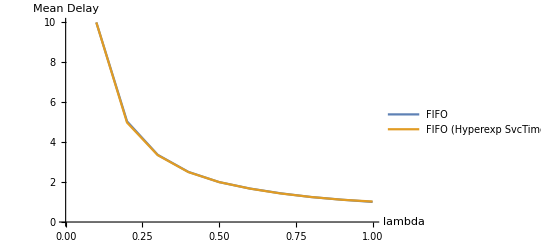

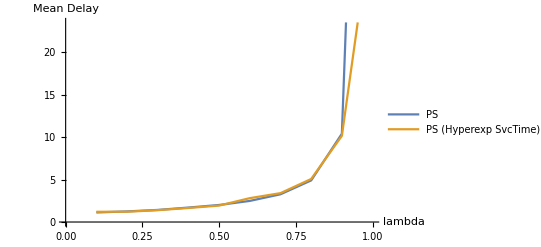

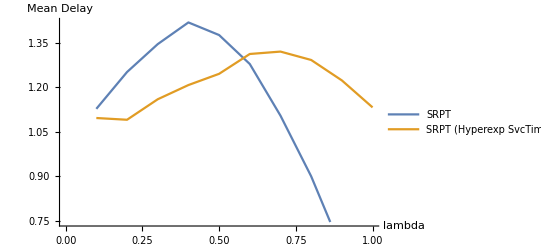

```mathematica
ListLinePlot[{Legended[data[[1]], "FIFO"], Legended[data[[4]], "FIFO (Hyperexp SvcTime)"]} , AxesLabel-> {"lambda", "Mean Delay"}]
ListLinePlot[{Legended[data[[2]], "PS"], Legended[data[[5]], "PS (Hyperexp SvcTime)"]} , AxesLabel-> {"lambda", "Mean Delay"}]
ListLinePlot[{Legended[data[[3]], "SRPT"], Legended[data[[6]], "SRPT (Hyperexp SvcTime)"]} , AxesLabel-> {"lambda", "Mean Delay"}]
```

Here we see that SRPT is most affected by the different distribution of the service time, while PS and FIFO remain roughly the same.

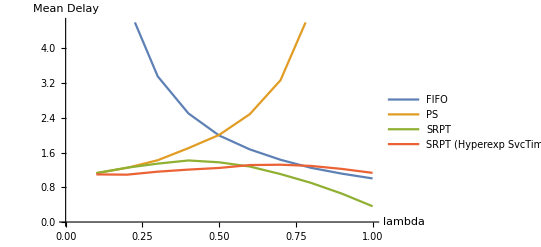

```mathematica
ListLinePlot[{Legended[data[[1]], "FIFO"], Legended[data[[2]], "PS"],Legended[data[[3]], "SRPT"], Legended[data[[6]], "SRPT (Hyperexp SvcTime)"]}
 , AxesLabel-> {"lambda", "Mean Delay"}]
```

We can see the affect of increase/decreasing arrival rate has for throughput. 
1) FIFO works well with higher arrival rate
2) PS works well with lower arrival rate
3) SRPT remain relatively constant as compared to FIFO and PS.

## Question 3 Modified 3-class M/G/1 PS simulator class-3 flows arrive according to the Poisson process with rate λ_3

the flows are served at
rate r 3 bit/s. In your implementation you may assume that the sizes L 3 are exponentially
distributed (and hence the service times, as well), similarly as in the example code. Make the
necessary modifications by following the example implementation of the 2-class simulator.

```mathematica
simulator3classPS[la1_,la2_,la3_,mu1_,mu2_,mu3_,iniTrans_,simuLen_]:=
Module[{simTime,meanqlen,prevEvTime,nextArr,nextDep,
joblist1,joblist2,joblist3,
delsum1,delsum2,delsum3,
nofsamples1,nofsamples2,nofsamples3,
nn1,nn2,nn3,depInd,
deptime1,deptime2,deptime3,
i,latot,p},
simTime=0;
latot=la1+la2+la3;
nextArr=RandomVariate[ExponentialDistribution[latot]];
nextDep=Infinity;
joblist1={};joblist2={};joblist3={};
meanqlen=0;
delsum1=0;delsum2=0;delsum3=0;
nofsamples1=0;nofsamples2=0;nofsamples3=0;
nn1=0; (* nof flows for class 1 *)
nn2=0; (* nof flows for class 2 *)
nn3=0; (* nof flows for class 3 *)
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime;
simTime=nextArr;
meanqlen+=(nn1+nn2+nn3)*(Min[simTime,simuLen]-prevEvTime);
(* serve flows *)
If[nn1>0,
For[i=1,i≤Length[joblist1],i++,
joblist1[[i,2]]=joblist1[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist1={}];
If[nn2>0,
For[i=1,i≤Length[joblist2],i++,
joblist2[[i,2]]=joblist2[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist2={}];
If[nn3>0,
For[i=1,i≤Length[joblist3],i++,
joblist3[[i,2]]=joblist3[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist3={}];
(* insert new arrival *)
(* Probability that the arrival is from class k is then simply la_k/la1 + la2 + ... + la_k*)
p = RandomReal[];
Which[
p<la1/(la1+la2+la3),
{
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}];
joblist1=Sort[joblist1,#1[[2]]<#2[[2]]&];
nn1++;
},
la1/(la1+la2+la3)  <=p  <  (la1+la2)/(la1+la2+la3),
{
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}];
joblist2=Sort[joblist2,#1[[2]]<#2[[2]]&];
nn2++;
},
p>=(la1+la2)/(la1+la2+la3),
{
joblist3=Append[joblist3,{simTime,RandomVariate[ExponentialDistribution[mu3]]}];
joblist3=Sort[joblist3,#1[[2]]<#2[[2]]&];
nn3++;
}
];
(* update arrival event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[latot]];
(* update departure event, there is at least 1 flow in system *)
If[nn1>0,deptime1=simTime+joblist1[[1,2]]*(nn1+nn2+nn3),deptime1=Infinity];
If[nn2>0,deptime2=simTime+joblist2[[1,2]]*(nn1+nn2+nn3),deptime2=Infinity];
If[nn3>0,deptime3=simTime+joblist3[[1,2]]*(nn1+nn2+nn3),deptime3=Infinity];
Which[
deptime1 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime1;
depInd=1;},
deptime2 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime2;
depInd=2;},
deptime3 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime3;
depInd=3;}
];
},
{
prevEvTime=simTime;
simTime=nextDep;
meanqlen+=(nn1+nn2+nn3)*(Min[simTime,simuLen]-prevEvTime);
(* serve flows *)
If[nn1>0,
For[i=1,i≤Length[joblist1],i++,
joblist1[[i,2]]=joblist1[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist1={}];
If[nn2>0,
For[i=1,i≤Length[joblist2],i++,
joblist2[[i,2]]=joblist2[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist2={}];
If[nn3>0,
For[i=1,i≤Length[joblist3],i++,
joblist3[[i,2]]=joblist3[[i,2]]-(simTime-prevEvTime)/(nn1+nn2+nn3)]
,joblist3={}];
(* collect statistics *)
Which[
depInd==1,
{If[simTime>iniTrans,
delsum1+=(simTime-joblist1[[1,1]]);
nofsamples1++;
];
joblist1=Delete[joblist1,1];
nn1--;},
depInd==2,
{If[simTime>iniTrans,
delsum2+=(simTime-joblist2[[1,1]]);
nofsamples2++;
];
joblist2=Delete[joblist2,1];
nn2--;},
depInd==3,
{If[simTime>iniTrans,
delsum3+=(simTime-joblist3[[1,1]]);
nofsamples3++;
];
joblist3=Delete[joblist3,1];
nn3--;}
];
(* update departure event, now system may be totally empty *)
If[nn1>0,deptime1=simTime+joblist1[[1,2]]*(nn1+nn2),deptime1=Infinity];
If[nn2>0,deptime2=simTime+joblist2[[1,2]]*(nn1+nn2),deptime2=Infinity];
If[nn3>0,deptime3=simTime+joblist3[[1,2]]*(nn1+nn2),deptime3=Infinity];
If[(nn1+nn2+nn3)>0,
Which[
deptime1 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime1;
depInd=1;},
deptime2 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime2;
depInd=2;},
deptime3 == Min[deptime1, deptime2, deptime3],
{nextDep=deptime3;
depInd=3;}
],
nextDep=Infinity
];
}
];
];
{meanqlen/(latot*simuLen),(delsum1+delsum2+delsum3)/(nofsamples1+nofsamples2+nofsamples3),delsum1/nofsamples1,delsum2/nofsamples2,delsum3/nofsamples3}
]
```

The sizes in all classes obey the same exponential distribution with mean 1 Mbit, i.e., E[L] = 1Mbit.

The service bit rates of all classes are r_1 = 10 Mbit/s, r_2 = 5 Mbit/s and r 3 =_1
Mbit/s.

 Also, we fix the arrival rate of classes 1 and 2, such that λ_1 = 3 and λ_2 = 0.5.
 
 Simulate the system as a function of λ 3 = {0.05, 0.1, 0.3, 0.5} and estimate the throughput
of of each class together with the 95% confidence intervals.

```mathematica
mu1 = 10; mu2 = 5; mu3 = 1;
la1 = 3; la2 = 0.5; la3 = 0.5;
lambda3 = {0.05,0.1,0.3,0.5};

data = {};
For[ix=1, ix≤ Length[lambda3], ix++,
la3 = lambda3[[ix]];
res = Table[simulator3classPS[la1,la2,la3,mu1,mu2,mu3,200,2000], {10}];
resultTable = Append[resultTable, res];
Print[StringForm["When λ = ``", la3]];
means = {};
For[i = 3,  i≤ 5, i++, 
mean = Mean[res[[All,i]]];
ci = MeanCI[res[[All,i]]];
Print[StringForm["Class = ``, Mean: ``, 95% Confidence Interval = ``",i-2,NumberForm[mean, 5], ci]];
means = Append[means, {la3, mean}];
];
data = Append[data, means];
];
```

When λ = 0.05

Class = 1, Mean: 0.16898, 95% Confidence Interval = {0.164213,0.173748}

Class = 2, Mean: 0.33085, 95% Confidence Interval = {0.318502,0.343207}

Class = 3, Mean: 0.44963, 95% Confidence Interval = {0.410203,0.48905}

When λ = 0.1

Class = 1, Mean: 0.17399, 95% Confidence Interval = {0.171089,0.176899}

Class = 2, Mean: 0.35107, 95% Confidence Interval = {0.34203,0.360116}

Class = 3, Mean: 0.51215, 95% Confidence Interval = {0.466399,0.557896}

When λ = 0.3

Class = 1, Mean: 0.19908, 95% Confidence Interval = {0.191094,0.207072}

Class = 2, Mean: 0.41861, 95% Confidence Interval = {0.3842,0.45302}

Class = 3, Mean: 0.61758, 95% Confidence Interval = {0.536182,0.69897}

When λ = 0.5

Class = 1, Mean: 0.23479, 95% Confidence Interval = {0.218596,0.250982}

Class = 2, Mean: 0.49502, 95% Confidence Interval = {0.442669,0.547376}

Class = 3, Mean: 0.82992, 95% Confidence Interval = {0.647927,1.01191}

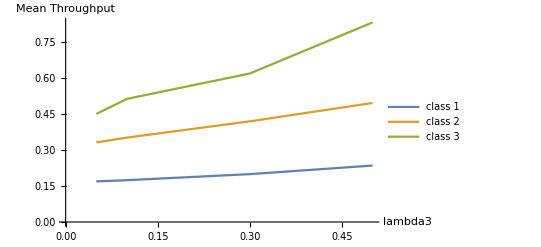

```mathematica
y1 = data[[All, 1]];  y2 = data[[All, 2]]; y3 = data[[All, 3]];
ListLinePlot[{Legended[y1, "class 1"], Legended[y2, "class 2"], Legended[y3, "class 3"]}, AxesLabel-> {"lambda3", "Mean Delay"}]
```